```mathematica
data1={{1,2},{2,3},{3,4},{4,5},{5,7},{6,9},{7,11},{8,12},{9,19},{10,21},{11,22},{12,24},{13,26},{14,30},{15,31},{16,37},{17,38},{18,41},{19,42},{20,45},{21,46}};
```

```mathematica
a=46;
m= a*(1-(β/(β-1+a^{t^b}))^α);
```

```mathematica
fit = FindFit[data1, m, {b,α,β},t]
```

```mathematica
β=41.71 (*експоненциално разпределение*) 
α=0.0024
 a=46
 b=1.8
H[t_]:=a*(1-(β/(β-1+a^{t^b}))^α)
H1[t_]:=b*Log[a]*t^{b-1}*a^{t^b}
H2[t_]:=a
g1=Plot[H[t],{t,0.1,22},PlotRange->{0,50},AspectRatio->0.6,PlotStyle->{Red}];(*фунцията на стойностите на откритите грешки до момента*)
g2=Plot[H1[t],{t,0.1,22},PlotRange->{0,50},AspectRatio->0.6,PlotStyle->{Blue}];(*функция на откриване на неизправности,зависещи от времето*)
g3=Plot[H2[t],{t,0.1,22},PlotRange->{0,50},AspectRatio->0.6,PlotStyle->{Dashed}];(*общият брой нагрешките в софтуера*)
```

41.71

0.0024

46

1.8

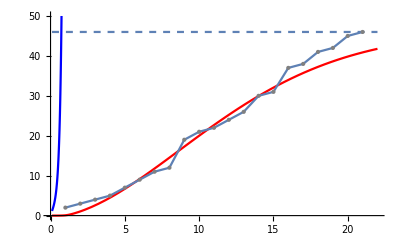

```mathematica
Show[g1,g2,g3, ListPlot[data1, Joined -> True, Mesh -> Full, MeshStyle-> Directive[PointSize[Large], Thick, Gray]]]
```